## Bee plot

```mathematica
ρ=0.0;ss=400;slope=.5;
```

```mathematica
slope2=-.1;
```

```mathematica
xd=Table[RandomVariate[MultinormalDistribution[{2,2},{{1,ρ},{ρ,1}}]],{ss}];
```

```mathematica
e=Table[RandomVariate[MultinormalDistribution[{1},{{1}}]],{ss}];
```

```mathematica
epsilon = Table[RandomVariate[NormalDistribution[0,.1]],{ss}];
```

```mathematica
lp=Plot[x,{x,0,4}];
```

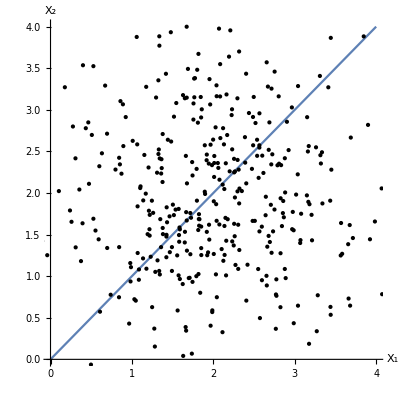

```mathematica
Show[lp,Graphics[Point/@xd],AspectRatio->1,AxesLabel->{"X_1","X_2"}]
```

```mathematica
y=xd.Transpose[{{slope,slope2}}] + epsilon;
```

```mathematica
f[x_]:=slope*x;
```

```mathematica
f[x_,r_]:=slope*x+slope2*r;
```

```mathematica
f2[x_,r_]:=.3*x+.1*r;
```

```mathematica
pts=Join[xd,y,2];
```

```mathematica
plane=Plot3D[f[x,r],{x,0,4},{r,0,4},AxesLabel->{"X_2","X_1","Y"},AspectRatio->1,Mesh->None,AspectRatio->1];
```

```mathematica
plane2=Plot3D[f2[x,r],{x,0,4},{r,0,4},AxesLabel->{"X_2","X_1","Y"},AspectRatio->1,Mesh->None,AspectRatio->1,ColorFunction->Green];
```

```mathematica
planeAxis=Show[plane,Graphics3D[{Thick,Line[{{0,0,-1/2},{0,0,3}}]}]]
```

-Graphics3D-

```mathematica
projection1[x_]:=Block[{z},z=x; z[[1]]=0;Line[{x,z}]];
```

```mathematica
projectiony[x_]:=Block[{z},z=x; z[[3]]=0;Line[{x,z}]];
```

```mathematica
Show[plane,Graphics3D[Point/@pts],AspectRatio->1,BoxRatios->{1,1,1},AxesLabel->{"X_2","X_1","Y"}]
```

-Graphics3D-

## Multicollinearity

```mathematica
ρ=0.97;ss=400;slope=.5;
```

```mathematica
slope2=-.1;
```

```mathematica
xd=Table[RandomVariate[MultinormalDistribution[{2,2},{{1,ρ},{ρ,1}}]],{ss}];
```

```mathematica
e=Table[RandomVariate[MultinormalDistribution[{1},{{1}}]],{ss}];
```

```mathematica
epsilon = Table[RandomVariate[NormalDistribution[0,.1]],{ss}];
```

```mathematica
lp=Plot[x,{x,0,4}];
```

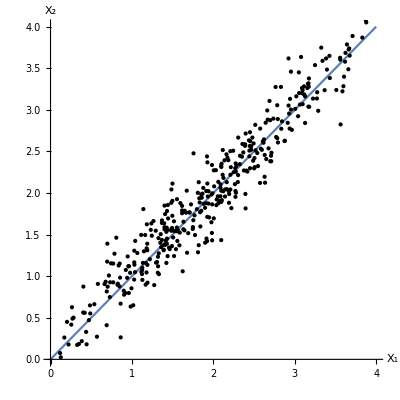

```mathematica
Show[lp,Graphics[Point/@xd],AspectRatio->1,AxesLabel->{"X_1","X_2"}]
```

```mathematica
y=xd.Transpose[{{slope,slope2}}] + epsilon;
```

```mathematica
f[x_]:=slope*x;
```

```mathematica
f[x_,r_]:=slope*x+slope2*r;
```

```mathematica
f2[x_,r_]:=.3*x+.1*r;
```

```mathematica
pts=Join[xd,y,2];
```

```mathematica
plane=Plot3D[f[x,r],{x,0,4},{r,0,4},AxesLabel->{"X_2","X_1","Y"},AspectRatio->1,Mesh->None,AspectRatio->1];
```

```mathematica
plane2=Plot3D[f2[x,r],{x,0,4},{r,0,4},AxesLabel->{"X_2","X_1","Y"},AspectRatio->1,Mesh->None,AspectRatio->1,ColorFunction->Green];
```

```mathematica
projection1[x_]:=Block[{z},z=x; z[[1]]=0;Line[{x,z}]];
```

```mathematica
projectiony[x_]:=Block[{z},z=x; z[[3]]=0;Line[{x,z}]];
```

```mathematica
Show[plane,Graphics3D[Point/@pts],AspectRatio->1,BoxRatios->{1,1,1},AxesLabel->{"X_2","X_1","Y"}]
```

-Graphics3D-

```mathematica
multicollin=Show[plane,plane2,Graphics3D[Point/@pts],AspectRatio->1,BoxRatios->{1,1,1},AxesLabel->{"X_2","X_1","Y"}]
```

-Graphics3D-

```mathematica
Export["multicollin.png",multicollin];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["multicollin.png"]]]
```

```mathematica
Show[plane,Graphics3D[{projection1/@pts,projectiony/@pts}],AspectRatio->1,BoxRatios->{1,1,1},AxesLabel->{"X_1","X_2","Y"}]
```

-Graphics3D-

## Redundant regressors

```mathematica
Σ={{Subscript[σ, X]^2,Subscript[σ, XW]},{Subscript[σ, XW],Subscript[σ, X]^2}}
```

{{σ_X^2,σ_XW},{σ_XW,σ_X^2}}

```mathematica
corr=Subscript[σ, XW]-> Subscript[ρ, XW]*Subscript[σ, X]*Subscript[σ, W]
```

σ_XW→ρ_XW σ_W σ_X

```mathematica
Inverse[Σ]/.corr//Simplify
```

{{1/(-ρ_XW^2 σ_W^2+σ_X^2),(ρ_XW σ_W)/(ρ_XW^2 σ_W^2 σ_X-σ_X^3)},{(ρ_XW σ_W)/(ρ_XW^2 σ_W^2 σ_X-σ_X^3),1/(-ρ_XW^2 σ_W^2+σ_X^2)}}